```mathematica
Clear["Global`*"];

(* constants *)
(* TODO - probably put this in a constants file somewhere that I can easily access *)
G = 6.67*10^-8; (* universal gravitational constant in cgs units *)
MPluto = 1.29*10^25; (* mass of Pluto in g *)
μ = 20; (*g/mol; mean molecular weight of Pluto's atmosphere from NASA factsheet*)

R=8.3145; (*J/mol K; universal gas constant*)
T = 50; (* Kelvin; assumed constant, following NASA factsheet, for now*)
rSurf = 1195000000; (*cm; surface radius of Pluto*)
dPluto = 4.864*10^15;  (*cm; distance from Earth to Pluto (1989 value from Elliot et al paper) *)
```

```mathematica
(* assumptions *)
T = 100; (* Kelvin; assumed temperature for isothermal atmosphere *)

(* using these values for now *)
rH = rSurf;
nH = 0.02504*10^31; (* ideal gas number density *)
v = 13.4*10^5; (* velocity of the star that is normal to the limb of Pluto *)
```

```mathematica
(*function definitions *)
nFunc[r_]:=nH*E^((G*MPluto*μ)/(R*T)*(1/r-1/rH)); (* Elliot et al. 1989 eq 1*)
gFunc[r_]:=G*MPluto/r^2;
HFunc[r_]:= (R*T)/(μ*gFunc[r]); (* Elliot et al. 1989 eq 2*)
```

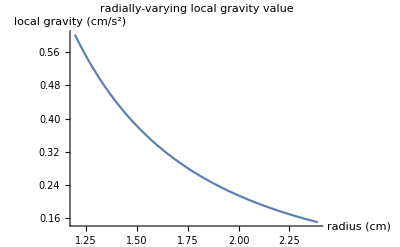

```mathematica
(* radially-varying local gravity *)
g = gFunc[r];
Plot[g,{r,rSurf,rSurf*2},AxesLabel-> {"radius (cm)", "local gravity (cm/s^2)"},PlotLabel-> "radially-varying local gravity value"]
```

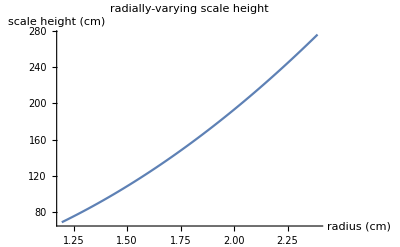

```mathematica
(* radially-varying scale height *)
H = HFunc[r];
Plot[H,{r,rSurf,rSurf*2},AxesLabel-> {"radius (cm)", "scale height (cm)"},PlotLabel-> "radially-varying scale height"]
```

```mathematica
(* radially-varying number density *)
Plot[nFunc[r],{r,rSurf,HFunc[rH]+rSurf},AxesLabel-> {"radius (cm)", "n"},PlotLabel-> "radially-varying number density"]
```

-Graphics-

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0.0418933}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ϕ→1/(1+ProductLog[ⅇ^(1+t)])}}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{ϕ→1/(1+ProductLog[ⅇ^(1-t)])}}

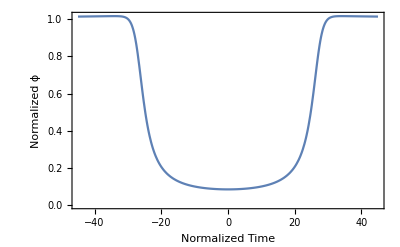

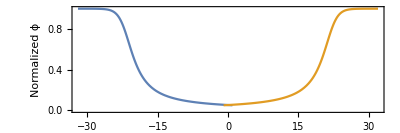

```mathematica
Hh = HFunc[rH];
HObs =Hh*(1-0.5*(Hh/rH)+(59/8)*(Hh/rH)^2);
hObs = HObs/v;

phi2T[ϕ_] :=1/ϕ-2+Log[1/ϕ-1];
N[Solve[phi2T[x]-25== -phi2T[x]+25,x]]
Solve[t ==1/ϕ-2+Log[1/ϕ-1],ϕ]
Solve[-t ==1/ϕ-2+Log[1/ϕ-1],ϕ]

s = 25;

Plot[1/(1+ProductLog[E^(1+(t+25))])+1/(1+ProductLog[E^(1-(t-25))]),{t,-45,45},Frame->True,FrameLabel->{"Normalized Time", "Normalized ϕ"}]
ParametricPlot[{{phi2T[Subscript[ϕ, ref]]-20,Subscript[ϕ, ref]},{-phi2T[Subscript[ϕ, ref]]+20,Subscript[ϕ, ref]}},{Subscript[ϕ, ref],0.05,1},AspectRatio->1/3,AxesLabel->{"(t-t_ref)/h_obs","Normalized ϕ"},Frame->True,FrameLabel->{"Normalized Time", "Normalized ϕ"}]
(* number of scale heights from half light *)
```